```mathematica
Get["/Users/tomeichlersmith/Desktop/Summer Research 2016/Necessary Functions.m"]
```

{pluck, peak, parametricregion, egsystem, QOtriangleApprox, QOtriangleApprox2, freqsintens, graphfi, keep, loudfreqs, graphweight, colorfreqs, freqband, freqlines, print3Dborder, print3Dregion, p, vard, disvector}

### StackExchange Code

```mathematica
arcgen[{p1_,p2_,p3_},r_,n_]:=Module[{dc=Normalize[p1-p2]+Normalize[p3-p2],cc,th},cc=p2+r dc/EuclideanDistance[dc,Projection[dc,p1-p2]];
th=Sign[Det[PadRight[{p1,p2,p3},{3,3},1]]] (π-VectorAngle[p3-p2,p1-p2])/(n-1);
NestList[RotationTransform[th,cc],p2+Projection[cc-p2,p1-p2],n-1]];

roundedPolygon[Polygon[pts_?MatrixQ],r_?NumericQ,n:(_Integer?Positive):12]:=Polygon[Flatten[arcgen[#,r,n]&/@Partition[If[TrueQ[First[pts]==Last[pts]],Most,Identity][pts],3,1,{2,-2}],1]];
```

pts is list of vertex points (in order)
r is rounding radius
n is fineness of curve

### Interpolation of Points

New function called roundedPoints that outputs the points used to construct the Polygon

```mathematica
roundedPoints[pts_?MatrixQ,r_?NumericQ,n:(_Integer?Positive):12]:=
Flatten[arcgen[#,r,n]&/@
Partition[If[TrueQ[First[pts]==Last[pts]],Most,Identity][pts],3,1,{2,-2}],
1];
```

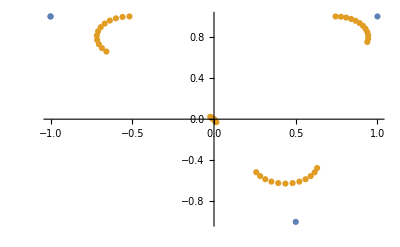

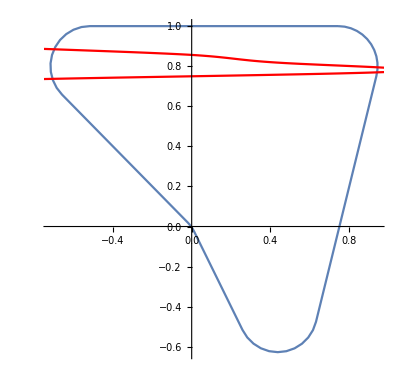

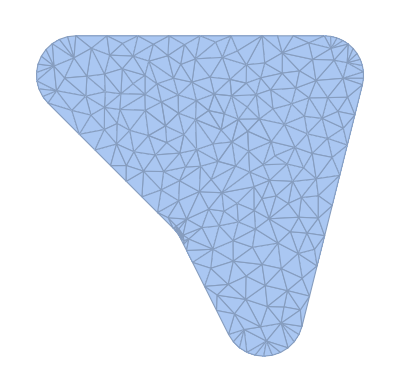

```mathematica
Module[{points,points1,points2,repeat,intx,inty,fst,intx1,inty1,pplot,pplot1,repeat1},
points={{-1,1},{0.5,-1},{1,1},{0,0}};
fst=FindShortestTour[points];
points1=points[[fst[[2]]]];
points2=roundedPoints[points1,1/5];
Print[ListPlot[{points1,points2}]];
repeat=Join[points2,points2];
repeat1=Join[points1,points1,points1];
intx=Interpolation[repeat[[All,1]],Method->"Spline",InterpolationOrder->1];
inty=Interpolation[repeat[[All,2]],Method->"Spline",InterpolationOrder->1];
intx1=Interpolation[repeat1[[All,1]],Method->"Spline"];
inty1=Interpolation[repeat1[[All,2]],Method->"Spline"];
pplot=ParametricPlot[{intx[u],inty[u]},{u,Length[points2],2Length[points2]}];
pplot1=ParametricPlot[{intx1[u],inty[u]},{u,Length[points1],2Length[points1]},PlotStyle->Red];
Print[Show[pplot,pplot1]];
DiscretizeRegion[roundedPolygon[Polygon[N[points1]],1/5]]]
```